## Обработка результатов измерений лабораторной работы №36 “Определение тепловых свойств материалов методом регулярного режима”

#### Примечание : Калориметр 1 -водяная камера, калориметры 2 и 3 -воздушная камера

### Данные эксперимента: τ-время опыта t1 - t8 показания термопар в калориметрах и камерах: 1-2-калориметр 1; 3-4 -калориметр 2; 5-6 калориметр 3; 7-воздушная камера; 8 - водяная камера.

```mathematica
τ=Quantity[Table[25+50*i,{i,0,34}],"Seconds"]
```

{25 s,75 s,125 s,175 s,225 s,275 s,325 s,375 s,425 s,475 s,525 s,575 s,625 s,675 s,725 s,775 s,825 s,875 s,925 s,975 s,1025 s,1075 s,1125 s,1175 s,1225 s,1275 s,1325 s,1375 s,1425 s,1475 s,1525 s,1575 s,1625 s,1675 s,1725 s}

```mathematica
t1=Quantity[{20.6,24.8,27.0,29.1,30.6,31.5,32.1,33.2,34.0,34.6,35.4,35.7,36.3,36.7,36.9,37.4,38.0,38.4,38.7,39.0,39.3,39.3,39.6,40.2,40.1,40.3,40.6,40.7,40.9,41.3,41.3,41.5,41.4,41.7,41.7},"DegreesCelsius"];
t2=Quantity[{21.8,22.2,23.1,27.0,25.5,26.6,27.3,28.4,29.5,30.4,31.5,32.4,33.4,34.1,35.3,36.0,36.7,37.5,36.1,33.5,39.0,39.6,39.9,40.5,40.7,41.0,41.4,41.7,42.0,42.2,42.5,42.8,42.9,43.1,43.2},"DegreesCelsius"];
t3=Quantity[{ 22.5,24.0,24.9,25.9,26.6,27.2,27.7,28.4,28.9,27.5,29.9,30.3,30.7,31.2,31.7,32.0,32.5,32.8,33.3,33.6,34.0,34.2,34.6,34.9,35.2,35.6,35.8,36.1,36.3,36.7,37.1,37.2,37.4,37.5,37.8},"DegreesCelsius"];
t4=Quantity[{22.1,22.6,23.2,24.0,24.6,25.2,25.7,26.5,26.9,27.7,28.2,28.7,29.0,29.5,30.1,30.5,31.1,31.3,31.9,32.2,32.7,33.0,33.4,33.7,34.0,34.4,34.8,35.1,35.2,35.6,36.0,36.2,36.5,36.7,36.8},"DegreesCelsius"];
t5=Quantity[{ 24.7,25.6,26.6,27.3,28.0,28.1,28.6,29.0,29.5,29.7,30.2,30.6,30.8,31.2,31.5,31.7,32.1,32.5,32.7,33.1,33.1,33.5,33.6,34.0,34.1,34.3,34.6,34.8,34.9,35.2,35.4,35.7,35.9,36.0,36.3},"DegreesCelsius"];
t6=Quantity[{ 25.6,26.6,27.5,28.0,28.6,29.0,29.6,29.9,30.1,30.6,31.0,31.2,31.4,31.9,32.3,32.4,32.8,33.1,33.4,33.6,33.8,34.0,34.2,34.6,34.7,35.0,35.2,35.3,35.5,35.8,36.0,36.2,36.6,36.7,36.8},"DegreesCelsius"];
t7=Quantity[{41.3,41.0,41.0,40.7,40.8,41.0,41.2,41.1,41.1,41.2,41.3,41.3,41.3,41.3,41.4,41.6,41.6,41.7,41.8,41.9,41.8,41.8,41.8,41.9,41.9,41.9,42.1,45.1,42.1,42.3,42.1,42.3,42.3,42.3,42.4},"DegreesCelsius"];
t8=Quantity[{ 44.7,44.7,44.8,44.7,44.7,44.8,44.7,44.9,44.9,44.8,44.9,44.9,44.8,44.7,44.8,44.8,44.8,44.9,44.8,44.9,44.7,44.7,44.8,44.7,44.8,44.8,44.9,44.9,44.7,44.9,44.9,44.9,44.9,44.8,44.9},"DegreesCelsius"];
```

### θ-разность температур какой-либо точки тела и среды. Учитывая что К1-водяная камера, а К2 К3- воздушная,найдем ln(θ_(1-6)) ,где θ_(1,2) для калориметра в водяной камере а остальные для калориметров воздушных камерах

```mathematica
lnθ1=Log[QuantityMagnitude[t8-t1]]
```

{2.95491,2.7213,2.54945,2.38876,2.26176,2.16332,2.02815,1.93152,1.91692,1.8718,1.80829,1.75786,1.62924,1.64866,1.62924,1.50408,1.4816,1.45862,1.41099,1.36098,1.30833,1.30833,1.22378,1.16315,0.955511,1.16315,1.06471,0.955511,0.955511,0.832909,0.832909,0.832909,0.693147,0.741937,0.641854}

```mathematica
lnθ2=Log[QuantityMagnitude[t8-t2]]
```

{3.10009,3.08649,3.08191,3.03495,2.99072,2.92316,2.83908,2.76632,2.73437,2.70136,2.65324,2.60269,2.5337,2.50144,2.40695,2.37955,2.34181,2.32239,2.25129,2.2192,2.16332,2.11626,2.05412,1.98787,1.96009,1.90211,1.82455,1.79176,1.75786,1.70475,1.62924,1.56862,1.52606,1.50408,1.45862}

```mathematica
lnθ3=Log[QuantityMagnitude[t7-t3]]
```

{2.89591,2.85647,2.82138,2.79117,2.76632,2.73437,2.70136,2.68102,2.66723,2.66026,2.63906,2.63189,2.63189,2.60269,2.58776,2.58776,2.57261,2.55723,2.5337,2.5416,2.5177,2.5096,2.5096,2.47654,2.47654,2.48491,2.47654,2.44235,2.44235,2.43361,2.40695,2.40695,2.41591,2.3979,2.3979}

```mathematica
lnθ4=Log[QuantityMagnitude[t7-t4]]
```

{2.92316,2.91235,2.90142,2.8848,2.8792,2.85647,2.83908,2.82731,2.81541,2.80336,2.79728,2.77882,2.78501,2.76001,2.75366,2.74727,2.73437,2.71469,2.71469,2.70136,2.68785,2.68785,2.68102,2.65324,2.65324,2.66026,2.63906,2.6174,2.62467,2.60269,2.59525,2.58776,2.57261,2.56495,2.56495}

```mathematica
lnθ5=Log[QuantityMagnitude[t7-t5]]
```

{2.90142,2.85071,2.81541,2.78501,2.75366,2.71469,2.68102,2.66026,2.64617,2.62467,2.61007,2.59525,2.58776,2.56495,2.54945,2.5337,2.5177,2.5177,2.48491,2.47654,2.4681,2.45101,2.44235,2.4248,2.41591,2.40695,2.38876,2.36085,2.36085,2.33214,2.33214,2.32239,2.31254,2.29253,2.27213}

```mathematica
lnθ6=Log[QuantityMagnitude[t7-t6]]
```

{2.89591,2.85071,2.8094,2.77882,2.73437,2.70805,2.67415,2.64617,2.63189,2.6174,2.61007,2.57261,2.57261,2.55723,2.54945,2.5177,2.5096,2.50144,2.47654,2.4681,2.44235,2.43361,2.43361,2.41591,2.3979,2.3979,2.37955,2.35138,2.35138,2.34181,2.32239,2.29253,2.28238,2.27213,2.26176}

#### Изобразим зависимости lnθ_(1-6)(τ)

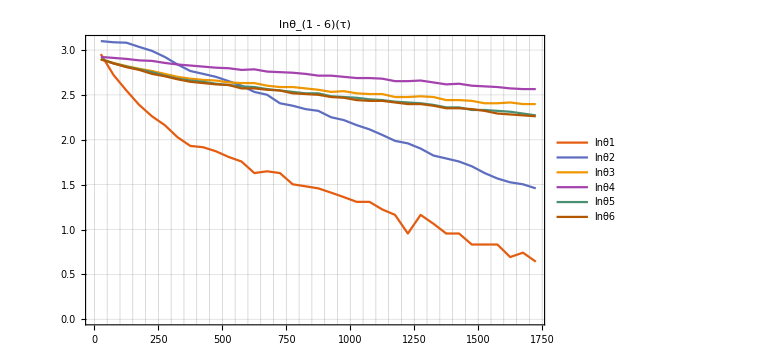

```mathematica
bufferlnθ[i_]:=Table[{QuantityMagnitude[τ[[j]]],Evaluate[ToExpression["lnθ"<>ToString[i]][[j]]]},{j,1,Length[τ]}];
ListLinePlot[Map[bufferlnθ,Range[1,6]],GridLines->{Range[0,1750,50],Range[0,4,0.1]},PlotLabel->"lnθ_(1 - 6)(τ)",PlotTheme->"Scientific",PlotLegends->{"lnθ1","lnθ2","lnθ3","lnθ4","lnθ5","lnθ6"},ImageSize->Large]
```

#### Изобразим отдельно графики для каждого калориметра для поиска участков линейной зависимости:

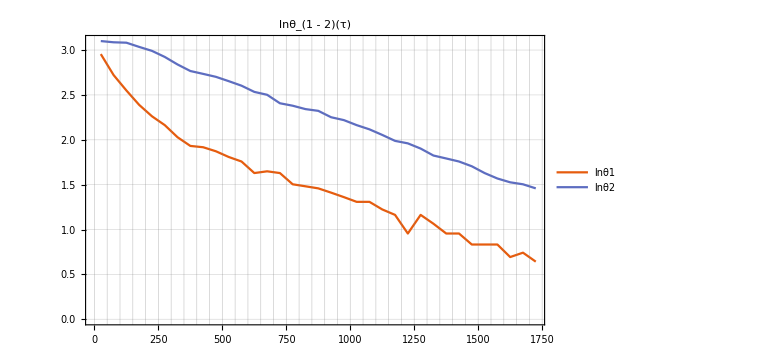

```mathematica
ListLinePlot[Map[bufferlnθ,Range[1,2]],GridLines->{Range[0,1750,50],Range[0,4,0.1]},PlotLabel->"lnθ_(1 - 2)(τ)",PlotTheme->"Scientific",PlotLegends->{"lnθ1","lnθ2"},ImageSize->Large]
```

#### Линейный участок :325-1750 s (τ7-τ35) для первого калориметра

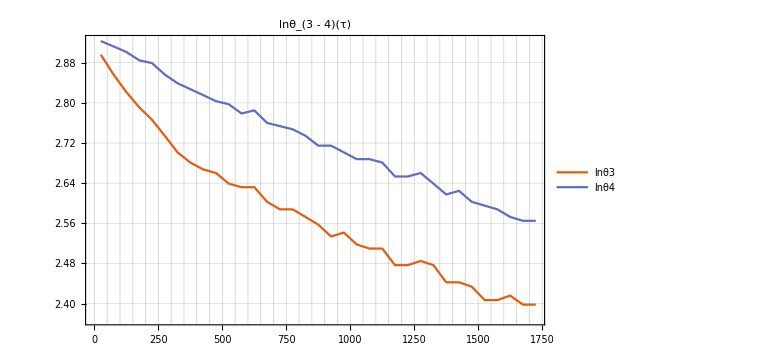

```mathematica
ListLinePlot[Map[bufferlnθ,Range[3,4]],GridLines->{Range[0,1750,50],Range[0,3,0.05]},PlotLabel->"lnθ_(3 - 4)(τ)",PlotTheme->"Scientific",PlotLegends->{"lnθ3","lnθ4"},ImageSize->Large]
```

#### Линейный участок : 625-1750 s (τ13-τ35) для второго калориметра

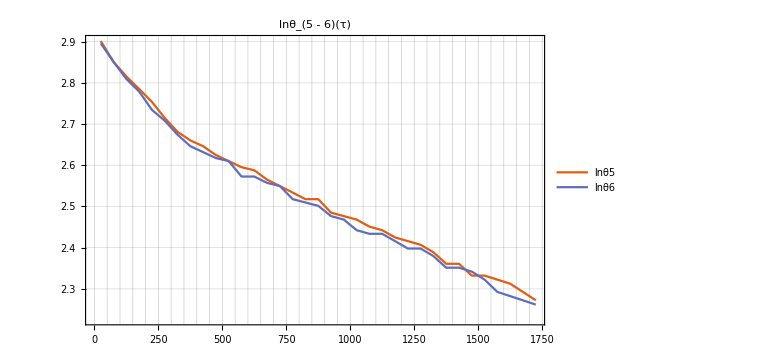

```mathematica
ListLinePlot[Map[bufferlnθ,Range[5,6]],GridLines->{Range[0,1750,50],Range[0,4,0.05]},PlotLabel->"lnθ_(5 - 6)(τ)",PlotTheme->"Scientific",PlotLegends->{"lnθ5","lnθ6"},ImageSize->Large]
```

#### Линейный участок : 525-1250 s (τ11-τ25) для третьего калориметра

#### Введем данные о калориметрах: Mcuprum-масса медного (эталонного)калориметра (kg) ccuprum- удельная теплоемкость меди (J/(Kg*K)) Mob- масса медной оболочки калориметра №2 (kg) Di- диаметр i-го калориметра (m) Zi-высота i-го калориметра(m) D2inner-внутренний диаметр калориметра №2 (m) Z2inner-внутренний диаметр калориметра №2(m)

```mathematica
Mcuprum=Quantity[0.23,"Kilograms"];
ccuprum=Quantity[390,("Joules")/("Kilograms"*"Kelvins")];
Mob=Quantity[0.073,"Kilograms"];
D1=Quantity[0.04,"Meters"];
Z1=Quantity[0.06,"Meters"];
D2=Quantity[0.0294,"Meters"];
Z2=Quantity[0.054,"Meters"];
D2inner=Quantity[0.0286,"Meters"];
Z2inner=Quantity[0.0532,"Meters"];
D3=Quantity[0.0294,"Meters"];
Z3=Quantity[0.054,"Meters"];
```

#### Найдем темп нагрева калориметров m1-относится к первому калориметру , m11- по значениям с первой термопары, m12 по значениям со второй термопары и т.д.

```mathematica
m11=(lnθ1[[7]]-lnθ1[[35]])/QuantityMagnitude[τ[[35]]-τ[[7]]]
```

0.00099021

```mathematica
m12=(lnθ2[[7]]-lnθ2[[35]])/QuantityMagnitude[τ[[35]]-τ[[7]]]
```

0.000986045

```mathematica
m21=(lnθ3[[13]]-lnθ3[[35]])/QuantityMagnitude[τ[[35]]-τ[[13]]]
```

0.000212721

```mathematica
m22=(lnθ4[[13]]-lnθ4[[35]])/QuantityMagnitude[τ[[35]]-τ[[13]]]
```

0.000200056

```mathematica
m31=(lnθ5[[11]]-lnθ5[[35]])/QuantityMagnitude[τ[[35]]-τ[[11]]]
```

0.00028162

```mathematica
m32=(lnθ6[[11]]-lnθ6[[35]])/QuantityMagnitude[τ[[35]]-τ[[11]]]
```

0.000290256

#### Найдем коэффициенты формы калориметров 1 и 2

```mathematica
K1=(5.783/(D1/2)^2+9.87/Z1^2)^-1
```

0.0000581424 m^2

```mathematica
K2=(5.783/(D2inner/2)^2+9.87/Z2inner^2)^-1
```

0.0000314788 m^2

#### Найдем коэффицент температуропроводности исследуемого материала для калориметра №1 , используя темп нагрева m_∞=m1 и число Фурье(при τ=τ35)

```mathematica
a1=Quantity[QuantityMagnitude[K1*m11],("Meters"^2)/("Seconds")]
```

5.75732×10^-8 m^2/s

```mathematica
Fo=a1*τ[[35]]/(D1/2)^2
```

0.248284

#### Определим значения коэффициента неравномерности температурного распределения ψ 2 для калориметра № 2 Для этого найдем M и воспользуемся таблицей зависимости ψ(M):

```mathematica
M2=QuantityMagnitude[m21*K2/a1]
```

0.116308

```mathematica
M21=0.110;ψ21=0.918;M22=0.123;ψ22=0.905;
```

#### Проинтерполируем и найдем наше значение ψ 2 :

```mathematica
Mψ=Interpolation[{{0.110,0.918},{0.123,0.905}},InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
ψ2=Mψ[M2]
```

0.911692

#### Полная теплоемкость калориметра №2 равна сумме теплоемкостей исследуемого материала и оболочки калориметра с учетом коэффициента неравномерности температурного поля, т.е C_2=C_(2,и)+ψ_2 C_(2,об), при этом площади внешний поверхностей калориметров № 2 и № 3 и коэффициенты теплоотдачи с наружных поверхностей равны. Найдем теплоемкость исследуемого материала:

```mathematica
C2i=(ccuprum*Mcuprum*m31/m21-ccuprum*Mob)*ψ2
```

82.3103 J/K

#### Найдем теплоемкость оболочки калориметра:

```mathematica
C2ob=ccuprum*Mob*ψ2
```

25.9559 J/K

#### Найдем полную теплоемкость калориметра № 2: (можно так же просто сложить теплоемкость исследуемого материала и оболочки калориметра № 2 )

```mathematica
C2=ccuprum*Mcuprum*m31/m21*ψ2
```

108.266 J/K

#### Рассчитаем коэффициент теплопроводности λ=a*c_(2,и)*ρ_(2,и)=|C_(2,и)=c_(2,и)*M_(2,и)|=a*(C_(2,и))/(V_(2,и)),где a-коэффициент температуропроводности исследуемого материала,определенный в эксперименте с калориметром №1 (a=a1) (m^2/s); ρ_(2,и)- плотность исследуемого материала (kg/m^3); V_(2,и)-объем исследуемого материала, определяемый по внутренним размерам калориметра № 2 (m^3) ; Сначала найдем объем исследуемого материала:

```mathematica
V2i=π*(D2inner/2)^2*Z2inner
```

0.000034177 m^3

#### Теперь найдем коэффициент теплопроводности λ (с учетом оболочки):

```mathematica
λwithBoundryLayerIncluded=UnitConvert[a1*C2i/V2i,("Watts")/("Meters"*"Kelvins")]
```

0.138657 W/(m K)

#### Теперь найдем коэффициент теплопроводности λ (без учета оболочки):

```mathematica
V2=π*(D2/2)^2*Z2;λwithBoundryLayerNotIncluded=UnitConvert[a1*C2/V2,("Watts")/("Meters"*"Kelvins")]
```

0.170034 W/(m K)

#### Проверим выполнение условия о стремлении числа Био к бесконечности (Bi→∞) для калориметра № 1. Для этого решим для точки r=0 уравнение (1) относительно μ_1 Уравнение (1): θ = (t_ж-t_(r=0))/(t_ж-t_0)=(2 J_1(μ_1))/(μ_1*(J_0^2(μ_1)+J_1^2(μ_1)))*ⅇ^(-μ_1^2*Fo),где J_0,J_1- функции Бесселя первого рода нулевого и первого порядка соотвественно. t_ж-температура водяной камеры в τ_0 , t_(r=0) -температура t_2 в τ_0 , t_0-температура t_1 в τ_0

```mathematica
θ=(44.3-25.1)/(44.3-22.1)
```

0.864865

#### Решим уравнение (1) численно относительно μ_1 :

```mathematica
FindRoot[θ==(2*BesselJ[1,μ1])/(μ1*((BesselJ[0,μ1])^2+(BesselJ[1,μ1])^2))*Exp[-μ1^2*Fo],{μ1,3}]; μ1
```

μ1

#### Имеем μ 1 = 3.24246. При μ 1 >2.405 Bi→∞. Условие выполнено.

#### Определим температуру отнесения для a и λ по формуле (2) Формула (2) : t_отн=(t_(k,2)+t_ж)/2, где t_ж-температура среды в термостате (°C);t_(k,2)-температура калориметра № 2 в начале эксперимента (°C)

```mathematica
tRelative=UnitConvert[(t8[[1]]+t2[[1]])/2,"DegreesCelsius"]
```

33.2 °C

#### Построим распределение температуры по сечению калориметра № 1 на стадии регулярного режима. Выбираем τ[7],τ[15],τ[25] как три момента времени при наступлении регулярного режима.

```mathematica
t1τ={t8[[7]],t1[[7]],t2[[7]],t1[[7]],t2[[7]]};t2τ={t8[[15]],t1[[15]],t2[[15]],t1[[15]],t8[[15]]};t3τ={t8[[25]],t1[[25]],t2[[25]],t1[[25]],t8[[25]]};
r={-0.02,-0.02*0.707,0,0.02*0.707,0.02};
```

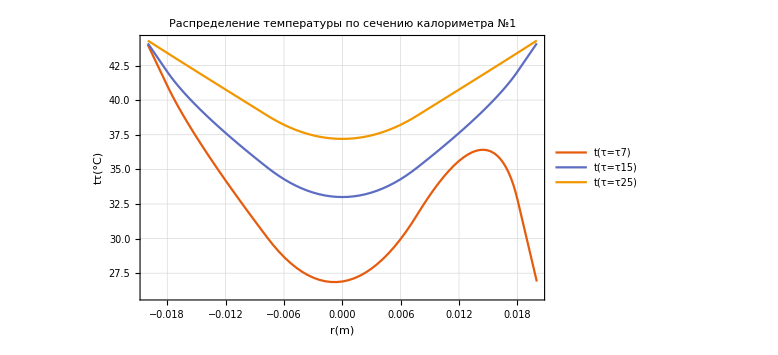

```mathematica
ListLinePlot[{Table[{r[[i]],t1τ[[i]]},{i,1,Length[t1τ]}],Table[{r[[i]],t2τ[[i]]},{i,1,Length[t2τ]}],Table[{r[[i]],t3τ[[i]]},{i,1,Length[t3τ]}]},InterpolationOrder->Automatic,PlotLabel->"Распределение температуры по сечению калориметра №1",PlotTheme->"Scientific",PlotLegends->{"t(τ=τ7)","t(τ=τ15)","t(τ=τ25)"},ImageSize->Large,GridLines->{Range[-0.02,0.02,0.0005],Range[25,45,0.5]},Frame->True,FrameLabel->{"r(m)","tτ(°C)"}]
```

#### Определим погрешности измерения тепловых свойств материала(λ и a)

```mathematica
ΔΔt=Quantity[0.1,"DegreesCelsius"];Δt1=Quantity[QuantityMagnitude[t8[[7]]-t1[[7]]],"DegreesCelsius"]
```

7.6 °C

```mathematica
Δt2=Quantity[QuantityMagnitude[t8[[35]]-t1[[35]]],"DegreesCelsius"]
```

1.9 °C

```mathematica
Δθ1=ΔΔt/Δt1
```

0.973286

```mathematica
Δθ2=ΔΔt/Δt2
```

0.993456

```mathematica
Δθ=Δθ1+Δθ2
```

1.96674

```mathematica
ΔΔτ=1;Δm1=√((Δθ/QuantityMagnitude[τ[[35]]-τ[[7]]])^2+((Exp[lnθ1[[7]]]-Exp[lnθ1[[35]]])/(QuantityMagnitude[τ[[35]]-τ[[7]]])^2*ΔΔτ)^2)
```

0.00140482

#### Определим погрешность вычисления коэффициента температуропроводности:

```mathematica
δa=Δm1/m11
```

1.41871

#### Табличное значение коэффициента теплопроводности

```mathematica
λStandard=Quantity[0.18,("Watts")/("Meters"*"Kelvins")]
```

0.18 W/(m K)

#### Разница если не учитывать оболочку:

```mathematica
ΔλwithBoundryLayerNotIncluded=Abs[λStandard-λwithBoundryLayerNotIncluded]
```

0.00996649 W/(m K)

#### Найдем погрешность коэффициента теплопроводности в случае если оболочка не учитывается:

```mathematica
δλwithBoundryLayerNotIncluded=ΔλwithBoundryLayerNotIncluded/λwithBoundryLayerNotIncluded
```

0.0586148

#### Найдем погрешность коэффициента теплопроводности в случае если оболочка учитывается:

```mathematica
ΔλwithBoundryLayerIncluded=Abs[λStandard-λwithBoundryLayerIncluded]
```

0.0413434 W/(m K)

```mathematica
δλWithBoundryLayerIncluded=ΔλwithBoundryLayerIncluded/λwithBoundryLayerIncluded
```

0.298171

#### Вывод: 1)Углублены знания о процессе нестационарной теплопроводности в твердых телах. Изучено влияние начального теплового состояния и условий теплообмена тела с окружающей средой на вид распределения температуры в теле. 2) Произведено ознакомление с нестационарными методами экспериментального определения теплофизических свойств материалов. 3)Освоен метод регулярного теплового режима,его экспериментальная реализация при определении коэффициентов теплопроводности и температуропроводности в условиях нагревания/охлаждения тела. 4)Произведен анализ полученных результатов и их сравнение со справочными данными.